## Packages import and definitions

```mathematica
Get[NotebookDirectory[]<>"../Mathematica_packages/QMB.wl"]
```

```mathematica
Get[NotebookDirectory[]<>"../Mathematica_packages/Chaometer.wl"]
```

```mathematica
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2
```

## Parameters setup

```mathematica
L=11(*number of spins*);
(*chaotic region*)
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
SeedRandom[1323];
ψ0=RandomChainProductState[L];
```

## Calculation

```mathematica
(*time points*)
numberOftemporalPoints=500;
tValues=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

```mathematica
AbsoluteTiming[
Module[{ψt},
sp=Table[
ψt=StateEvolution[t,ψ0,eigVals,eigVecs];
{t,SurvivalProbability[ψ0,ψt]},
{t,tValues}];
]
]
```

{81.113,Null}

```mathematica
ipr=Total[Abs[Conjugate[eigVecs].ψ0]^4]
```

0.00104983

```mathematica
numberOftemporalPoints=500;
tValues=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

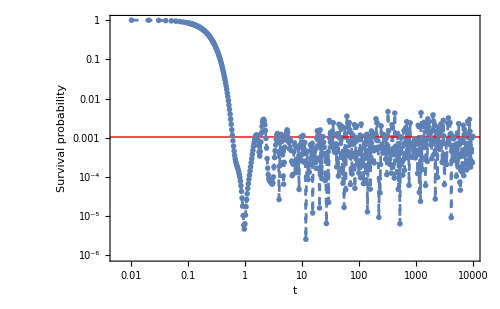

```mathematica
ListLogLogPlot[sp,
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","Survival probability"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500,
Epilog->{Red,InfiniteLine[{1,Log[ipr]},{1,0}]}]
```

```mathematica
Total[Abs[Conjugate[eigVecs].ψ0]^4]
```

0.00407137

```mathematica
Line[{{10^-4,ipr},{100,ipr}}]
```

Line[{{1/10000,0.00407137},{100,0.00407137}}]